```mathematica
∫(2r)/(r^2-2r+a^2)ⅆr
```

2 (ArcTan[(-1+r)/(√(-1+a^2))]/(√(-1+a^2))+1/2 Log[a^2-2 r+r^2])

```mathematica
tKSshift=2 (ArcTanh[((1-r)/(√(1-a^2)))^-1]/(√(+1-a^2))+1/2 Log[a^2-2 r+r^2])
```

2 (ArcTanh[(√(1-a^2))/(1-r)]/(√(1-a^2))+1/2 Log[a^2-2 r+r^2])

```mathematica
∫a/(r^2-2r+a^2)ⅆr
```

(a ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))

```mathematica
ϕKSshift=(a ArcTanh[((1-r)/(√(1-a^2)))^-1])/(√(1-a^2))
```

(a ArcTanh[(√(1-a^2))/(1-r)])/(√(1-a^2))

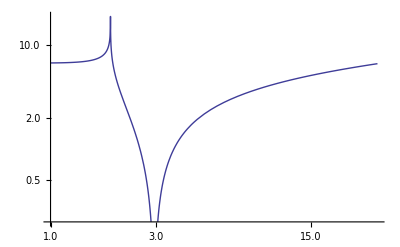

```mathematica
LogLogPlot[{Abs[tKSshift]/.{a->0.5}},{r,1,30}]
```

```mathematica
(* phiks = pjibl + ... *)
```

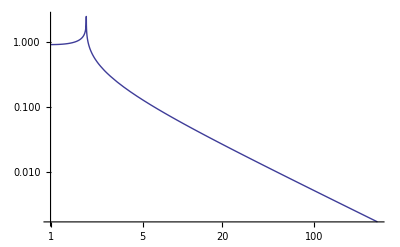

```mathematica
LogLogPlot[{Abs[ϕKSshift]/.{a->0.5}},{r,1,300}]
```

```mathematica
(****** testing *******)
```

```mathematica
vv1=∫1/(r^2-2r+0^2)ⅆr
```

1/2 Log[2-r]-Log[r]/2

```mathematica
vv1=∫1/(r^2-2r+a^2)ⅆr
```

ArcTan[(-1+r)/(√(-1+a^2))]/(√(-1+a^2))

```mathematica
ArcTan[I 3]
```

ⅈ ArcTanh[3]

```mathematica
ArcTan[3]//N
ArcTan[I 3]//N
```

1.24905

1.5708+0.346574 ⅈ

```mathematica
ArcTan[(-1+r)/(√(-1+a^2))]/(√(-1+a^2))/.{a->0.5,r->5}
ArcTanh[(1-r)/(√(1-a^2))]/(√(1-a^2))/.{a->0.5,r->5}
ArcTanh[((1-r)/(√(1-a^2)))^-1]/(√(1-a^2))/.{a->0.5,r->5}
```

-0.25402+1.8138 ⅈ

-0.25402+1.8138 ⅈ

-0.25402

```mathematica
NIntegrate[1/(r^2-2r+a^2)/.{a->0.5},{r,Infinity,5}]
```

-0.25402

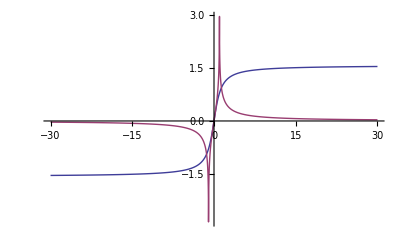

```mathematica
Plot[{ArcTan[x],Re[ArcTanh[1/x]]},{x,-30,30}]
```

```mathematica
(****** testing *******)
```